```mathematica
Clear["Global`*"];
ffCartPendulumGeneral[n_,τ_,τ1_,A_]:=Module[{x,xdot,f,θ,θdot,λ1,λ2,λ3,λ4,Δt,bcs,eqns,sv,froot,xff,xdotff,xff0,xdotff0,θff0,θdotff0,uff0,θff,θdotff,uff},Δt=τ/n;
f[{x_,xdot_,θ_,θdot_,λ1_,λ2_,λ3_,λ4_}]:={xdot,1/(1-A Cos[θ]^2)(A θdot^2 Sin[θ]+1/(1-A Cos[θ]^2)(λ4 Cos[θ]-λ2)+A Cos[θ] Sin[θ]),θdot,1/(1-A Cos[θ]^2)(-1/(1-A Cos[θ]^2)(-λ2 Cos[θ]+λ4 Cos[θ]^2)-Sin[θ]-A θdot^2 Cos[θ] Sin[θ]),0,-λ1,2/(A Cos[2 θ]+A-2)^3 (Cos[θ] (4 Sin[θ] (A λ4^2 Cos[2 θ]+4 A λ2^2+(A+2) λ4^2)-(A Cos[2 θ]-3 A+2) (A Cos[2 θ]+A-2) (A θdot^2 λ2-λ4))+A ((A-2) Cos[2 θ]+A) (A Cos[2 θ]+A-2) (λ2-θdot^2 λ4)-4 λ2 λ4 Sin[θ] (3 A Cos[2 θ]+3 A+2)),4/(A Cos[2 θ]+A-2)(A θdot Sin[θ] (λ2-λ4 Cos[θ]))-λ3};
bcs={Subscript[x, 0]==Subscript[xdot, 0]==Subscript[x, n]==Subscript[xdot, n]==Subscript[θ, 0]==Subscript[θdot, 0]==Subscript[θdot, n]==0,Subscript[θ, n]==π};eqns=Flatten[Join[bcs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}==1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}],{i,1,n}]]];sv=Flatten[Table[{{Subscript[x, i],0},{Subscript[xdot, i],0},{Subscript[θ, i],0},{Subscript[θdot, i],0},{Subscript[λ1, i],0},{Subscript[λ2, i],0},{Subscript[λ3, i],0},{Subscript[λ4, i],0}},{i,0,n}],1];froot=FindRoot[eqns,sv];
xff0=ListInterpolation[Table[Subscript[x, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->1];
xdotff0=ListInterpolation[Table[Subscript[xdot, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->1];θff0=ListInterpolation[Table[Subscript[θ, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->1];θdotff0=ListInterpolation[Table[Subscript[θdot, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->1];uff0=ListInterpolation[Table[1/(1-A Cos[Subscript[θ, i]]^2)(Subscript[λ4, i] Cos[Subscript[θ, i]]-Subscript[λ2, i]),{i,0,n}]/.froot,{0,τ},InterpolationOrder->1];

xff[t_]:=Piecewise[{{xff0[t],0≤t≤τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0≤t≤τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0≤t≤τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0≤t≤τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0≤t≤τ}},0];

{xff,xdotff,θff,θdotff,uff}]
```

Test the approximate solution on the open-loop dynamics

```mathematica
TestSwingUpGeneral[τ_,τ1_,uff0_,A_]:=Module[{eq,init,x,xdot,θ,θdot,xs,xdots,θs,θdots,t},
eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2)(uff0[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2)(-Sin[θ[t]]-Cos[θ[t]] (uff0[t]+A θdot[t]^2 Sin[θ[t]]))};
init={x[0]==xdot[0]==θ[0]==θdot[0]==0};
{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
{xs,θs,xdots,θdots}]
```

Show that linear feedback can stabilize against “bad” numerics

```mathematica
TestSwingUpGeneralFB[τ_,τ1_,xff0_,xdotff0_,θff0_,θdotff0_,uff0_,A_]:=Module[{eq,init,θ,θdot,θff,θdotff,x,xdot,xff,xdotff,uff,t,κ1,κ2,κ3,κ4,ufb,u,θs,θdots,xs,xdots,us},
κ1=κ2=3;  (* lqr for q=r for balancing pendulum *)
κ3 = -0.1;κ4 = -0.65;
xff[t_]:=Piecewise[{{xff0[t],0≤t≤τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0≤t≤τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0≤t≤τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0≤t≤τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0≤t≤τ}},0];
ufb[t_] := Piecewise[{{0,0≤t≤τ}},κ1(θff[t]-θ[t])+κ2 (θdotff[t]-θdot[t])+κ3(xff[t]-x[t])+κ4 (xdotff[t]-xdot[t])];
u[t_]:=uff[t]+ufb[t];
eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2)(u[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2)(-Sin[θ[t]]-Cos[θ[t]] (u[t]+A θdot[t]^2 Sin[θ[t]]))};
init={x[0]==xdot[0]==θ[0]==θdot[0]==0};
{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
us[t_]:=uff[t]+Piecewise[{{0,0≤t≤τ}},κ1(θff[t]-θs[t])+κ2 (θdotff[t]-θdots[t])+κ3(xff[t]-xs[t])+κ4 (xdotff[t]-xdots[t])];;
{xs,θs,us}]
```

Add Feedback Numerically

```mathematica
CalculateGains[xff0_,xdotff0_,θff0_,θdotff0_,uff0_,A_]:=Module[{x,L,RHS,xdot,θ,θdot,u,K,S,soltn,i,j,s11,s12,s13,s14,s22,s23,s24,s33,s34,s44,Af,Bf,Q,fx,xState,ric,R,Mf,x2dot,θ2dot},
xState = {x,xdot,θ,θdot};
x2dot = 1/(1-A Cos[θ]^2)(u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]);
θ2dot= 1/(1-A Cos[θ]^2)(-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]));
fx = {xdot,x2dot,θdot,θ2dot};
L = 1/2*u^2;
Af = Grad[fx,xState]; (* For nD stuff use Grad*)
Bf = D[fx,u] ;(*For 1D stuff use D*)
Q = Grad[Grad[L,xState],xState];
Mf = Grad[D[L,u],xState];
R = D[L,{u,2}];
S = ({{s11, s12, s13, s14}, {s12, s22, s23, s24}, {s13, s23, s33, s34}, {s14, s24, s34, s44}});
ric =Q +  Afᵀ.S +S.Af -Outer[Times,S.Bf,Bfᵀ.S ] ; (* This is the Syntax for calculating Outer Products *)(*Q = I, M = 0, R = 1*)
RHS = Table[0,{i,4},{j,4}];
x = xff0;xdot = xdotff0;θ =θff0;θdot = θdotff0;u = uff0; (* Entering State Values *)
soltn = NMinimize[{1,ric == RHS},{s11,s12,s13,s14,s22,s23,s24,s33,s34,s44}][[2]];
S = S/.soltn;
K = Bfᵀ.S ;
K]
TestSwingUpGeneralFBNumeric[τ_,τ1_,xff0_,xdotff0_,θff0_,θdotff0_,uff0_,A_,KTable_,n_]:=Module[{K1,K2,K3,K4,eq,init,θ,θdot,θff,θdotff,x,xdot,xff,xdotff,uff,t,ufb,u,θs,θdots,xs,xdots,us,κ1,κ2,κ3,κ4},
κ1=κ2=3;  (* lqr for q=r for balancing pendulum *)
κ3 = -0.1;κ4 = -0.65;
K1[t_]:=Piecewise[Table[{KTable[[i]][[1]],(i-1)*τ/n <= t <= i*τ/n},{i,1,n}],KTable[[n]][[1]]];K2[t_]:=Piecewise[Table[{KTable[[i]][[2]],(i-1)*τ/n <= t <= i*τ/n},{i,1,n}],KTable[[n]][[2]]];K3[t_]:=Piecewise[Table[{KTable[[i]][[3]],(i-1)*τ/n <= t <= i*τ/n},{i,1,n}],KTable[[n]][[3]]];K4[t_]:=Piecewise[Table[{KTable[[i]][[4]],(i-1)*τ/n <= t <= i*τ/n},{i,1,n}],KTable[[n]][[4]]];
xff[t_]:=Piecewise[{{xff0[t],0≤t≤τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0≤t≤τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0≤t≤τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0≤t≤τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0≤t≤τ}},0];
ufb[t_]:=Piecewise[{{K3[t]*(θff[t]-θ[t])+K4[t] *(θdotff[t]-θdot[t])+K1[t]*(xff[t]-x[t])+K2[t] * (xdotff[t]-xdot[t]),0≤t≤τ}},κ1(θff[t]-θ[t])+κ2 (θdotff[t]-θdot[t])+κ3(xff[t]-x[t])+κ4 (xdotff[t]-xdot[t])];
u[t_]:=uff[t]+ufb[t];
eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2)(u[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2)(-Sin[θ[t]]-Cos[θ[t]] (u[t]+A θdot[t]^2 Sin[θ[t]]))};
init={x[0]==xdot[0]==θ[0]==θdot[0]==0};
{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
us[t_]:=uff[t]+Piecewise[{{K3[t]*(θff[t]-θs[t])+K4[t] *(θdotff[t]-θdots[t])+K1[t]*(xff[t]-xs[t])+K2[t] * (xdotff[t]-xdots[t]),0≤t≤τ}},κ1(θff[t]-θs[t])+κ2 (θdotff[t]-θdots[t])+κ3(xff[t]-xs[t])+κ4 (xdotff[t]-xdots[t])];
{xs,θs,us,K1,K2,K3,K4}]
```

Test example (Feedback turned on only at the end)

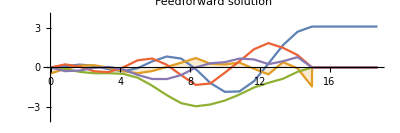

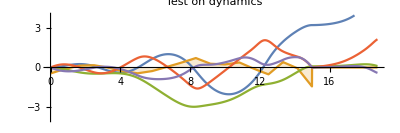

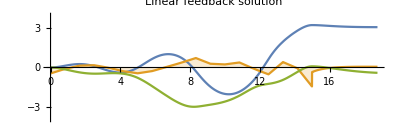

```mathematica
n=18;τ=15;τ1= τ*1.25 ;n2 = 40;
A=0.2; 
{x1a,xdot1a,θ1a,θdot1a,u1a}=ffCartPendulumGeneral[n,τ,τ1,A];  
{x1b,θ1b,xdot1b,θdot1b}=TestSwingUpGeneral[τ,τ1,u1a,A]; 
{x1c,θ1c,u1c}=TestSwingUpGeneralFB[τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A];
p1a=Plot[{θ1a[t],u1a[t],x1a[t],θdot1a[t],xdot1a[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->"Expressions",PlotLabel->"Feedforward solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1b=Plot[{θ1b[t],u1a[t],x1b[t],θdot1b[t],xdot1b[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->"Expressions",PlotLabel->"Test on dynamics",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1c=Plot[{θ1c[t],u1c[t],x1c[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->"Expressions",PlotLabel->"Linear feedback solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
```

Test example

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

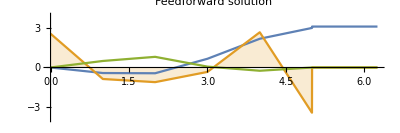
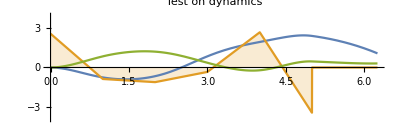
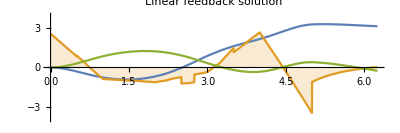
-Graphics- | -Graphics- | -Graphics-

```mathematica
n=5;τ=5;τ1= τ*1.25 ;n2 = 20;
A=0.2; 
{x1a,xdot1a,θ1a,θdot1a,u1a}=ffCartPendulumGeneral[n,τ,τ1,A];  
KTable = Table[CalculateGains[x1a[τ1/n2*i],xdot1a[τ1/n2*i],θ1a[τ1/n2*i],θdot1a[τ1/n2*i],u1a[τ1/n2*i],A],{i,0,n2}];
{x1b,θ1b,xdot1b,θdot1b}=TestSwingUpGeneral[τ,τ1,u1a,A]; 
{x1c,θ1c,u1c,K1,K2,K3,K4}=TestSwingUpGeneralFBNumeric[τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A,KTable,n2];
p1a=Plot[{θ1a[t],u1a[t],x1a[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->"Expressions",PlotLabel->"Feedforward solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}];
p1b=Plot[{θ1b[t],u1a[t],x1b[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->"Expressions",PlotLabel->"Test on dynamics",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}];
p1c=Plot[{θ1c[t],u1c[t],x1c[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->"Expressions",PlotLabel->"Linear feedback solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}];
pK1 = Plot[K1[t],{t,0,τ1}];
pK2 = Plot[K2[t],{t,0,τ1}];
pK3 = Plot[K3[t],{t,0,τ1}];
pK4 = Plot[K4[t],{t,0,τ1}];
Grid[{{p1a,p1b,p1c}}]
```

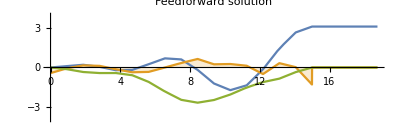
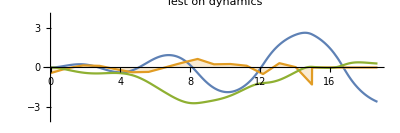
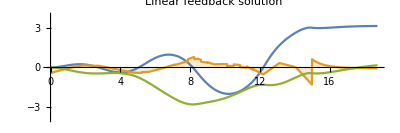
-Graphics- | -Graphics- | -Graphics-

```mathematica
n=16;τ=15;τ1= τ*1.25 ;n2 = 40;
A=0.2; 
{x1a,xdot1a,θ1a,θdot1a,u1a}=ffCartPendulumGeneral[n,τ,τ1,A];  
KTable = Table[CalculateGains[x1a[τ1/n2*i],xdot1a[τ1/n2*i],θ1a[τ1/n2*i],θdot1a[τ1/n2*i],u1a[τ1/n2*i],A],{i,0,n2}];
{x1b,θ1b,xdot1b,θdot1b}=TestSwingUpGeneral[τ,τ1,u1a,A]; 
{x1c,θ1c,u1c,K1,K2,K3,K4}=TestSwingUpGeneralFBNumeric[τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A,KTable,n2];
p1a=Plot[{θ1a[t],u1a[t],x1a[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->"Expressions",PlotLabel->"Feedforward solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}];
p1b=Plot[{θ1b[t],u1a[t],x1b[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->"Expressions",PlotLabel->"Test on dynamics",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}];
p1c=Plot[{θ1c[t],u1c[t],x1c[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->"Expressions",PlotLabel->"Linear feedback solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}];
pK1 = Plot[K1[t],{t,0,τ1}];
pK2 = Plot[K2[t],{t,0,τ1}];
pK3 = Plot[K3[t],{t,0,τ1}];
pK4 = Plot[K4[t],{t,0,τ1}];
Grid[{{p1a,p1b,p1c}}]
```

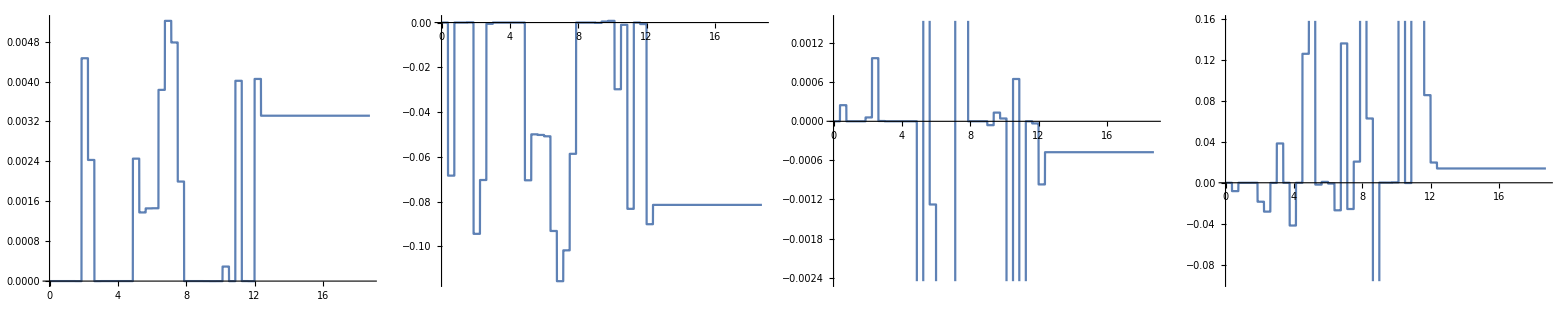

```mathematica
Grid[{{pK1,pK2,pK3,pK4}}]
```

Animation with General Cart-Pendulum swing up

```mathematica
AnimatePendulum[rules_]:=Animate[Evaluate[DrawSinglePendulum[x[t]/.rules,{θ[t]/.rules,1,1},t]],{t,0,τ1},DefaultDuration->5,AnimationRunning->False]
DrawSinglePendulum[cart_,{angle1_,length1_,mass1_},t_]:=
Module[{width1,density=30},
width1=mass1/length1/density;
Graphics[{
{Blue,Rectangle[{cart-1/4,-1/15},{cart+1/4,1/15}]},
{Orange,Translate[Rotate[Rectangle[{0,width1},{length1,-width1}],angle1-π/2,{0,0}],{cart,0}]}
},
PlotRange->2,ImageSize->280,
Frame->True,Axes->True,AxesStyle->Dashed,
PlotLabel->"t"==NumberForm[t,{4,2}]]]    
anim=Animate[Evaluate[DrawSinglePendulum[x1c[t],{θ1c[t],1,1},t]],{t,0,τ1},DefaultDuration->5,AnimationRunning->False,AnimationRepetitions->1]
```

```mathematica
(*SetDirectory["D:\\"];
Export["General_anim.avi",anim];*)
```

Test Feedback function

```mathematica
CalculateGains[xff0_,xdotff0_,θff0_,θdotff0_,uff0_,A_]:=Module[{x,L,RHS,xdot,θ,θdot,u,K,S,soltn,i,j,s11,s12,s13,s14,s22,s23,s24,s33,s34,s44,Af,Bf,Q,fx,xState,ric,R,Mf,x2dot,θ2dot},
xState = {x,xdot,θ,θdot};
x2dot = 1/(1-A Cos[θ]^2)(u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]);
θ2dot= 1/(1-A Cos[θ]^2)(-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]));
fx = {xdot,x2dot,θdot,θ2dot};
L = 1/2*u^2;
Af = Grad[fx,xState]; (* For nD stuff use Grad*)
Bf = D[fx,u] ;(*For 1D stuff use D*)
Q = Grad[Grad[L,xState],xState];
Mf = Grad[D[L,u],xState];
R = D[L,{u,2}];
S = ({{s11, s12, s13, s14}, {s12, s22, s23, s24}, {s13, s23, s33, s34}, {s14, s24, s34, s44}});
ric =Q +  Afᵀ.S +S.Af -Outer[Times,S.Bf,Bfᵀ.S ] ; (* This is the Syntax for calculating Outer Products *)(*Q = I, M = 0, R = 1*)
RHS = Table[0,{i,4},{j,4}];
x = xff0;xdot = xdotff0;θ =θff0;θdot = θdotff0;u = uff0; (* Entering State Values *)
soltn = NMinimize[{1,ric == RHS},{s11,s12,s13,s14,s22,s23,s24,s33,s34,s44}][[2]];
S = S/.soltn;
K = Bfᵀ.S ;
K]
```

```mathematica
n=5;τ=5;τ1= τ*1.25 ;
A=0.2; 
{x1a,xdot1a,θ1a,θdot1a,u1a}=ffCartPendulumGeneral[n,τ,τ1,A];  
KTable = Table[CalculateGains[x1a[τ/n*i],xdot1a[τ/n*i],θ1a[τ/n*i],θdot1a[τ/n*i],u1a[τ/n*i],A],{i,0,n}];
K1[t_]:=Piecewise[Table[{KTable[[i]][[1]],(i-1)*τ/n <= t <= i*τ/n},{i,1,n}],0];K2[t_]:=Piecewise[Table[{KTable[[i]][[2]],(i-1)*τ/n <= t <= i*τ/n},{i,1,n}],0];K3[t_]:=Piecewise[Table[{KTable[[i]][[3]],(i-1)*τ/n <= t <= i*τ/n},{i,1,n}],0];K4[t_]:=Piecewise[Table[{KTable[[i]][[4]],(i-1)*τ/n <= t <= i*τ/n},{i,1,n}],0];
xff[t_]:=Piecewise[{{x1a[t],0≤t≤τ}},0];
xdotff[t_]:=Piecewise[{{xdot1a[t],0≤t≤τ}},0];
θff[t_]:=Piecewise[{{θ1a[t],0≤t≤τ}},π];
θdotff[t_]:=Piecewise[{{θdot1a[t],0≤t≤τ}},0];
uff[t_]:=Piecewise[{{u1a[t],0≤t≤τ}},0];
ufb[t_] := Piecewise[{{K3[t]*(θff[t]-θ[t])+K4[t] *(θdotff[t]-θdot[t])+K1[t]*(xff[t]-x[t])+K2[t] * (xdotff[t]-xdot[t]),0≤t≤τ}},0];
u[t_]:=uff[t]+ufb[t];
eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2)(u[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2)(-Sin[θ[t]]-Cos[θ[t]] (u[t]+A θdot[t]^2 Sin[θ[t]]))};
init={x[0]==xdot[0]==θ[0]==θdot[0]==0};
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.